```mathematica
g2[τ_,τ0_,τ1_, g20_]=1-Exp[-Abs[τ]/τ1]+(1-g20)Exp[-Abs[τ]/τ0];
gaussian[τ_,σ_]=1/(σ √(2π))Exp[-1/2(τ/σ)^2];
gaussianNotNorm[τ_,σ_]=Exp[-1/2(τ/σ)^2];
```

```mathematica
Manipulate[Plot[g2[τ,τ0,τ1,g20],{τ,-5,5},PlotRange->{{-5,5},{0,2}}],{τ0,1,5},{τ1, 1, 10},{g20,0,1}]
```

```mathematica
Manipulate[Plot[gaussian[τ,σ],{τ,-5,5},PlotRange->{{-5,5},{0,2}}],{σ,1,5}]
```

```mathematica
Convolve[gaussian[τ,0.01],g2[τ,1,0.01],τ,ω]
```

39.8942 (0.0250663-0.99 (0.0125338 ⅇ^(-1. ω) Erfc[0.00707107-70.7107 ω]+0.0125338 ⅇ^(1. ω) Erfc[0.00707107+70.7107 ω]))

```mathematica
(*USE this one!*)g2Convolved[ω_,τ0_,τ1_,g20_,σ_]=Convolve[gaussian[τ,σ],g2[τ,τ0,τ1, g20],τ,ω]
```

1/(√(2 π) σ)((√(2 π))/(√(1/σ^2))-1/((σ^2-τ0 ω) (σ^2+τ0 ω))ⅇ^(σ^2/(2 τ0^2)-ω/τ0) (1-g20) √(π/2) (-√(1/σ^2) σ^6-ⅇ^((2 ω)/τ0) √(1/σ^2) σ^6+(τ0^2 ω^2)/(√(1/σ^2))+(ⅇ^((2 ω)/τ0) τ0^2 ω^2)/(√(1/σ^2))-σ^4 √(σ^2/τ0^2) τ0 Erf[(√(σ^2/τ0^2))/(√2)]-ⅇ^((2 ω)/τ0) σ^4 √(σ^2/τ0^2) τ0 Erf[(√(σ^2/τ0^2))/(√2)]+√(σ^2/τ0^2) τ0^3 ω^2 Erf[(√(σ^2/τ0^2))/(√2)]+ⅇ^((2 ω)/τ0) √(σ^2/τ0^2) τ0^3 ω^2 Erf[(√(σ^2/τ0^2))/(√2)]+√(1/σ^2) σ^6 Erf[1/(√2 √(1/σ^2) τ0)]+ⅇ^((2 ω)/τ0) √(1/σ^2) σ^6 Erf[1/(√2 √(1/σ^2) τ0)]-(τ0^2 ω^2 Erf[1/(√2 √(1/σ^2) τ0)])/(√(1/σ^2))-(ⅇ^((2 ω)/τ0) τ0^2 ω^2 Erf[1/(√2 √(1/σ^2) τ0)])/(√(1/σ^2))+σ^4 τ0 √(((σ^2-τ0 ω)^2)/(σ^2 τ0^2)) Erf[(√(((σ^2-τ0 ω)^2)/(σ^2 τ0^2)))/(√2)]+σ^2 τ0^2 ω √(((σ^2-τ0 ω)^2)/(σ^2 τ0^2)) Erf[(√(((σ^2-τ0 ω)^2)/(σ^2 τ0^2)))/(√2)]+ⅇ^((2 ω)/τ0) σ^4 τ0 √(((σ^2+τ0 ω)^2)/(σ^2 τ0^2)) Erf[(√(((σ^2+τ0 ω)^2)/(σ^2 τ0^2)))/(√2)]-ⅇ^((2 ω)/τ0) σ^2 τ0^2 ω √(((σ^2+τ0 ω)^2)/(σ^2 τ0^2)) Erf[(√(((σ^2+τ0 ω)^2)/(σ^2 τ0^2)))/(√2)])-1/(σ^2-τ1 ω)ⅇ^(σ^2/(2 τ1^2)-ω/τ1) √(π/2) (√(1/σ^2) σ^4+ⅇ^((2 ω)/τ1) √(1/σ^2) σ^4-(τ1 ω)/(√(1/σ^2))-(ⅇ^((2 ω)/τ1) τ1 ω)/(√(1/σ^2))+σ^2 √(σ^2/τ1^2) τ1 Erf[(√(σ^2/τ1^2))/(√2)]-√(σ^2/τ1^2) τ1^2 ω Erf[(√(σ^2/τ1^2))/(√2)]-√(1/σ^2) σ^4 Erf[1/(√2 √(1/σ^2) τ1)]+(τ1 ω Erf[1/(√2 √(1/σ^2) τ1)])/(√(1/σ^2))-σ^2 τ1 √(((σ^2-τ1 ω)^2)/(σ^2 τ1^2)) Erf[(√(((σ^2-τ1 ω)^2)/(σ^2 τ1^2)))/(√2)]-ⅇ^((2 ω)/τ1) σ^3 Erf[(σ^2+τ1 ω)/(√2 σ τ1)]+ⅇ^((2 ω)/τ1) σ τ1 ω Erf[(σ^2+τ1 ω)/(√2 σ τ1)]))

```mathematica
FullSimplify[g2Convolved[ω,τ0,τ1, g20,σ],Assumptions->{σ∈Reals,σ>0}]
```

1/2 ⅇ^(-((1/τ0+1/τ1) ω)) (2 ⅇ^((1/τ0+1/τ1) ω)-ⅇ^(σ^2/(2 τ0^2)+ω/τ1) (-1+g20) (Erfc[(σ^2-τ0 ω)/(√2 σ τ0)]+ⅇ^((2 ω)/τ0) Erfc[(σ^2+τ0 ω)/(√2 σ τ0)])-ⅇ^(σ^2/(2 τ1^2)+ω/τ0) Erfc[(σ^2-τ1 ω)/(√2 σ τ1)]-ⅇ^(ω/τ0+(σ^2+4 τ1 ω)/(2 τ1^2)) Erfc[(σ^2+τ1 ω)/(√2 σ τ1)])

```mathematica
(*Do NOT use this one!*)g2ConvolvedNotNorm[ω_,τ0_,g20_,σ_]=Convolve[gaussianNotNorm[τ,σ],g2[τ,τ0,g20],τ,ω]
```

(√(2 π))/(√(1/σ^2))+(ⅇ^(σ^2/(2 τ0^2)-ω/τ0) (1-g20) √(π/2) (-1-ⅇ^((2 ω)/τ0)+√(1/σ^2) σ Erf[(σ^2-τ0 ω)/(√2 σ τ0)]+ⅇ^((2 ω)/τ0) √(1/σ^2) σ Erf[(σ^2+τ0 ω)/(√2 σ τ0)]))/(√(1/σ^2))

```mathematica
g2Convolved[0,1,0.04,0.5]
```

0.328732

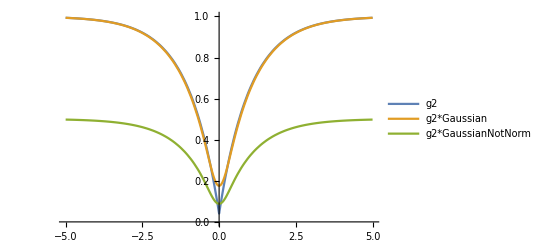

```mathematica
Plot[{g2[τ,1,0.04],g2Convolved[τ,1,0.04,0.2],g2ConvolvedNotNorm[τ,1,0.04,0.2]},{τ,-5,5},PlotLegends->{"g2","g2*Gaussian","g2*GaussianNotNorm"},PlotRange->{Automatic,{0,1}}]
```

Clearly we should used the normalized gaussian[]